```mathematica
(*nth prime*)
Prime[3]
```

5

```mathematica
(*shift enter to run code*)
Prime[9]
```

23

```mathematica
1+1
```

2

```mathematica
2*8
```

16

```mathematica
2^3
```

8

```mathematica
(*INTRO TO FUNCTIONS*)
RandomInteger[50]
```

```mathematica
3
?Fibonacci
```

3

```mathematica
(*FIRST LOOK AT LISTS*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5,10]
```

{5,6,7,8,9,10}

```mathematica
Range[3,21,2]
```

{3,5,7,9,11,13,15,17,19,21}

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[Range[5],Range[5,10]]
```

{1,2,3,4,5,5,6,7,8,9,10}

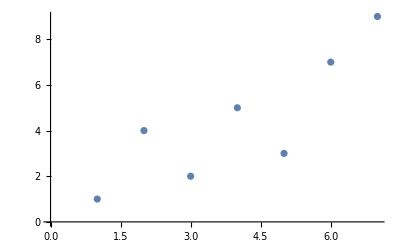

```mathematica
ListPlot[{1,4,2,5,3,7,9}]
```

```mathematica
Divisors[6]
```

{1,2,3,6}

```mathematica
Length[Divisors[6]]
```

4

```mathematica
Total[Divisors[6]](*sum of the list*)
```

12

```mathematica
Take[Range[10],4] (*returns the first values*)
```

{1,2,3,4}

```mathematica
Take[Range[10],-4] (*takes from the back*)
```

{7,8,9,10}

```mathematica
Drop[Range[10],3]
```

{4,5,6,7,8,9,10}

```mathematica
Part[Range[10],4] (*returns the nth element*)
```

4

```mathematica
(*DISPLAYING LISTS*)
(*ListLinePlot, BarChart, PieChart, PieChart3D, NumberLinePlot,*)   
(*If you place plots in a list then you can see them side by side. ROW and column to*)

(*OPERATIONS ON LISTS*)
 IntegerDigits[3454]
```

{3,4,5,4}

```mathematica
FromDigits[{1,3,2,4}]
```

```mathematica
1324
```

```mathematica
(*MAKING TABLES*)
Table["hello",9]
```

```mathematica
{"hello","hello","hello","hello","hello","hello","hello","hello","hello"}
(*COLORS & styles*)
 (*ColorNegate, Blend, RGBColor,  *)
```

```mathematica
Table[Lighter[Purple],10]
```

{RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666]}



```mathematica
(*Basic Graphics Objects*)
 Graphics[Circle[]]
```

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
(*Interactive Manipulation*)
Manipulate[n,{n,1,5,0.5}]
```

```mathematica
Column[Table[Green,n]]
```

Table::nliter: Non-list iterator n at position 2 does not evaluate to a real numeric value.

```mathematica
Manipulate[Column[Table[Green,n]],{n,1,5,0.5}]
```

```mathematica
(*Images Last Episode  *)
```

```mathematica
RandomImage[]
```

-Graphics-

-Graphics-

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
Binarize[-Graphics-]
```

-Graphics-

```mathematica
Clear
```

```mathematica
Circle[Most@centre,radius]
```

Most::normal: Nonatomic expression expected at position 1 in Most[centre].

Circle[Most[centre],radius]

```mathematica
Circle[{0,0,0},1]
```

Circle[{0,0,0},1]

```mathematica
Graphics[Circle[{0,0,0},1]]
```

-Graphics-

```mathematica
Graphics3D[{Thick,Red,circle3D[{0,0,0},2,{0,1,0}]}, Axes-> True]
```

-Graphics3D-

```mathematica
Graphics3D[{Thick,Green,circle3D[{0,0,0},2,{0,0,1},{0,Pi/2}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Thick,Purple,circle3D[{1,1,1},3,{0,1,1}]}]
```

-Graphics3D-

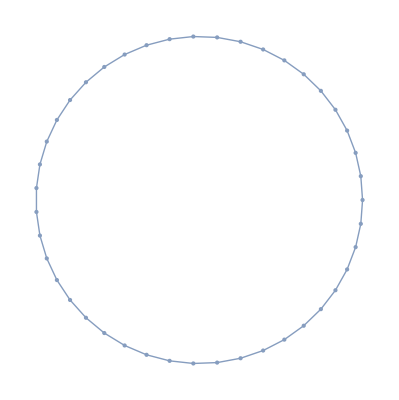

```mathematica
DiscretizeRegion[Circle [{0,0},1]]
```

```mathematica
MeshPrimitives[DiscretizeRegion[Circle [{0,0},1]], 1]
```

{Line[{{1.,0.},{0.989343,0.145601}}],Line[{{0.989343,0.145601},{0.957601,0.288099}}],Line[{{0.957601,0.288099},{0.905448,0.424457}}],Line[{{0.905448,0.424457},{0.833998,0.551768}}],Line[{{0.833998,0.551768},{0.744772,0.667319}}],Line[{{0.744772,0.667319},{0.639673,0.768647}}],Line[{{0.639673,0.768647},{0.52094,0.853593}}],Line[{{0.52094,0.853593},{0.391105,0.920346}}],Line[{{0.391105,0.920346},{0.252933,0.967484}}],Line[{{0.252933,0.967484},{0.109371,0.994001}}],Line[{{0.109371,0.994001},{-0.036522,0.999333}}],Line[{{-0.036522,0.999333},{-0.181637,0.983366}}],Line[{{-0.181637,0.983366},{-0.32288,0.94644}}],Line[{{-0.32288,0.94644},{-0.457242,0.889342}}],Line[{{-0.457242,0.889342},{-0.581859,0.81329}}],Line[{{-0.581859,0.81329},{-0.694074,0.719903}}],Line[{{-0.694074,0.719903},{-0.791496,0.611174}}],Line[{{-0.791496,0.611174},{-0.872049,0.489418}}],Line[{{-0.872049,0.489418},{-0.934016,0.357231}}],Line[{{-0.934016,0.357231},{-0.976076,0.21743}}],Line[{{-0.976076,0.21743},{-0.997332,0.0729953}}],Line[{{-0.997332,0.0729953},{-0.997332,-0.0729953}}],Line[{{-0.997332,-0.0729953},{-0.976076,-0.21743}}],Line[{{-0.976076,-0.21743},{-0.934016,-0.357231}}],Line[{{-0.934016,-0.357231},{-0.872049,-0.489418}}],Line[{{-0.872049,-0.489418},{-0.791496,-0.611174}}],Line[{{-0.791496,-0.611174},{-0.694074,-0.719903}}],Line[{{-0.694074,-0.719903},{-0.581859,-0.81329}}],Line[{{-0.581859,-0.81329},{-0.457242,-0.889342}}],Line[{{-0.457242,-0.889342},{-0.32288,-0.94644}}],Line[{{-0.32288,-0.94644},{-0.181637,-0.983366}}],Line[{{-0.181637,-0.983366},{-0.036522,-0.999333}}],Line[{{-0.036522,-0.999333},{0.109371,-0.994001}}],Line[{{0.109371,-0.994001},{0.252933,-0.967484}}],Line[{{0.252933,-0.967484},{0.391105,-0.920346}}],Line[{{0.391105,-0.920346},{0.52094,-0.853593}}],Line[{{0.52094,-0.853593},{0.639673,-0.768647}}],Line[{{0.639673,-0.768647},{0.744772,-0.667319}}],Line[{{0.744772,-0.667319},{0.833998,-0.551768}}],Line[{{0.833998,-0.551768},{0.905448,-0.424457}}],Line[{{0.905448,-0.424457},{0.957601,-0.288099}}],Line[{{0.957601,-0.288099},{0.989343,-0.145601}}],Line[{{0.989343,-0.145601},{1.,0.}}]}

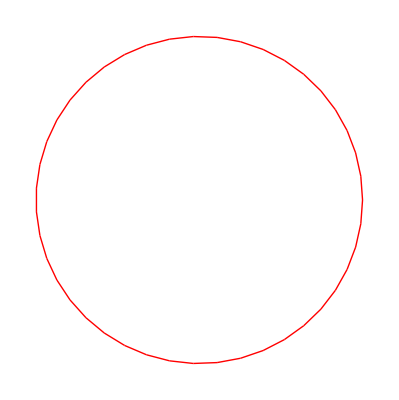

```mathematica
mesh=DiscretizeRegion[Circle[{0,0},1]];
Graphics[{Thick,Red,MeshPrimitives[mesh,1]}]
```

```mathematica
Graphics[{Thick,Red,Circle[{0,0},1]}]
```

```mathematica
expr={{{1,2},{3,4}},{{5,6},{7,8}}};
Level[expr,{-2}]
```

{{1,2},{3,4},{5,6},{7,8}}

```mathematica
Graphics3D[{Green,GeometricTransformation[Sphere[{0,0,0},1],RotationTransform[Pi,{1,0,0},{0,0,0}]]},Axes-> True]
```

-Graphics3D-

```mathematica
Graphics3D[{Arrow[{{0,0,0},{1,1,1}}],(*Original vector*)Blue,Arrow[{RotationTransform[Pi/3,{0,1,0}][#]&/@{{0,0,0},{1,1,1}}}]}]
```

```mathematica
Graphics3D[{Green,GeometricTransformation[Sphere[{0,0,0},1],RotationTransform[Pi,{1,0,0},{0,0,0}]]}, Axes-> True, AxesLabel -> {"x","y","z"}]
```

-Graphics3D-

```mathematica
Graphics3D[{Arrow[{{0,0,0},{1,1,1}}],(*Original vector*)Blue,Arrow[{RotationTransform[Pi/3,{0,1,0}][#]&/@{{0,0,0},{1,1,1}}}]}, Axes -> True, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Graphics3D[{Red,GeometricTransformation[Sphere[{0,0,0},1],TranslationTransform[{2,3,4}]]}, Axes -> True, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*Define Euler angles*)angles={0,Pi/8,Pi/8};  (*Rotate 30°,45°,60°*)

(*Compute Euler rotation matrix*)
eMatrix=EulerMatrix[angles,"ZYX"];

(*Define the cube shape*)
cube=Cuboid[{-1,-1,-1},{1,1,1}];

(*Apply Euler rotation to the cube*)
Graphics3D[{Opacity[0.3],Blue,cube,(*Original cube*)Red,GeometricTransformation[cube,eMatrix]  (*Rotated cube*)},Boxed->False, Axes -> True, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*Define Euler angles*)angles={Pi/4,Pi/3,Pi/6}; (*Rotate 45°,60°,30°*)

(*Compute Euler rotation matrix*)
eMatrix=EulerMatrix[angles,"XYZ"];

(*Define original coordinate axes*)
axes={Red,Arrow[{{0,0,0},{1,0,0}}],Green,Arrow[{{0,0,0},{0,1,0}}],Blue,Arrow[{{0,0,0},{0,0,1}}]};

(*Apply Euler rotation to axes*)
rotatedAxes=GeometricTransformation[axes,eMatrix];

Graphics3D[{Opacity[0.5],axes,rotatedAxes}, Axes -> True, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{Opacity[0.3],Blue,cube,(*Original cube*)Red,GeometricTransformation[cube,EulerMatrix[{t,t/2,t/3},"ZYX"]]},Boxed->False],{t,0,2 Pi}]
```

```mathematica
Graphics3D[{Blue,Tube[{{0,0,0},{1,1,1}},0.05]}]
```

-Graphics3D-